# Практикум №2. Структура выражения в Mathematica

Выполнил студент ММФ  БГУ
КМ, 1 к, 3 гр . Шпак А . В .
  03 октября 2021

## 1. Построение чистых функций.

### Задание 1.1

Постройте указанные многочлены:
а) однородный многочлен степени n от двух переменных c неопределенными
коэффициентами a[i ,j];
б) многочлен степени n от одной переменной с неопределенными
коэффициентами a[i].
в) многочлен степени n от двух переменных с неопределенными
коэффициентами a[i ,j]; 
Комментарии к решению: для каждого многочлена я использую один символ n (переменную n), посчитав такой стиль оформления решения корректным. 
Первый многочлен является однородным, так как каждый одночлен такого многочлена имеет одну и ту же степень, что и видно из примера. 
Второй многочлен имеет степень n, что так же видно из примера ниже. 
Третий многочлен не однородный, но так как в нём содержится две переменные x и y, то я записываю их со степенями такими же, как и в задании а), для того, чтобы в итоге получить многочлен степени n. Возможно в этом задании я бы мог использовать запись ∑_(i=1)^n a[i,i+10]x^1 y^(i-1) - тогда степень многочлена так же и останется n.

```mathematica
(*a)*)
n=4
p[n_]:=∑_(i=0)^n a[n-i,i] x^(n-i)y^i
p[n]
(*б)*)
f[n_]:=∑_(i=0)^n a[i] x^i
f[n]
(*в)*)
g[n_]:=∑_(i=0)^n a[i,i+3] x^i y^(n-i)
g[n]
Plus@@(f[#]&/@Range[0,n])
Plus@@(g[#]&/@Range[0,n])
```

4

y^4 a[0,4]+x y^3 a[1,3]+x^2 y^2 a[2,2]+x^3 y a[3,1]+x^4 a[4,0]

a[0]+x a[1]+x^2 a[2]+x^3 a[3]+x^4 a[4]

y^4 a[0,3]+x y^3 a[1,4]+x^2 y^2 a[2,5]+x^3 y a[3,6]+x^4 a[4,7]

5 a[0]+4 x a[1]+3 x^2 a[2]+2 x^3 a[3]+x^4 a[4]

a[0,3]+y a[0,3]+y^2 a[0,3]+y^3 a[0,3]+y^4 a[0,3]+x a[1,4]+x y a[1,4]+x y^2 a[1,4]+x y^3 a[1,4]+x^2 a[2,5]+x^2 y a[2,5]+x^2 y^2 a[2,5]+x^3 a[3,6]+x^3 y a[3,6]+x^4 a[4,7]

```mathematica
p[#]&/@Range[0,n]
```

{a[0,0],y a[0,1]+x a[1,0],y^2 a[0,2]+x y a[1,1]+x^2 a[2,0],y^3 a[0,3]+x y^2 a[1,2]+x^2 y a[2,1]+x^3 a[3,0],y^4 a[0,4]+x y^3 a[1,3]+x^2 y^2 a[2,2]+x^3 y a[3,1]+x^4 a[4,0]}

5

```mathematica
Plus@@(p[#]&/@Range[0,n])
```

a[0,0]+y a[0,1]+y^2 a[0,2]+y^3 a[0,3]+y^4 a[0,4]+x a[1,0]+x y a[1,1]+x y^2 a[1,2]+x y^3 a[1,3]+x^2 a[2,0]+x^2 y a[2,1]+x^2 y^2 a[2,2]+x^3 a[3,0]+x^3 y a[3,1]+x^4 a[4,0]

### Задание 1.2

Получите список мономов, которые содержатся в указанных многочленах:
а) однородный многочлен степени n от двух переменных c неопределенными
коэффициентами a[i ,j];
б) многочлен степени n от одной переменной с неопределенными
коэффициентами a[i].
в) многочлен степени n от двух переменных с неопределенными
коэффициентами a[i ,j]; 
Комментарии к решению: задание а) я решаю двумя способами. Первый способ: использую функцию Apply (@@). Так как результатом работы функции является замена head’а в выражении, а именно в нашем случае у суммы многочленов head’ом является Plus (процесс сложения одночленов), то на выходе мы получаем List (заменяем Plus) - список одночленов, входящих в многочлен. Проверяю на достоверность своё же утверждение с помощью функций FullForm, TreeForm, Head. Во втором способе я использую чистую функцию, посредством которой получаю тот же список. Задания б) и в) решаю так же, но уже без доказательства изменения head.

3

y^3 a[0,3]+x y^2 a[1,2]+x^2 y a[2,1]+x^3 a[3,0]

Plus[Times[Power[y,3],a[0,3]],Times[x,Power[y,2],a[1,2]],Times[Power[x,2],y,a[2,1]],Times[Power[x,3],a[3,0]]]

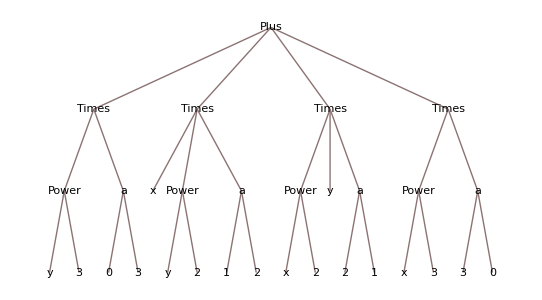

Plus

{y^3 a[0,3],x y^2 a[1,2],x^2 y a[2,1],x^3 a[3,0]}

List[Times[Power[y,3],a[0,3]],Times[x,Power[y,2],a[1,2]],Times[Power[x,2],y,a[2,1]],Times[Power[x,3],a[3,0]]]

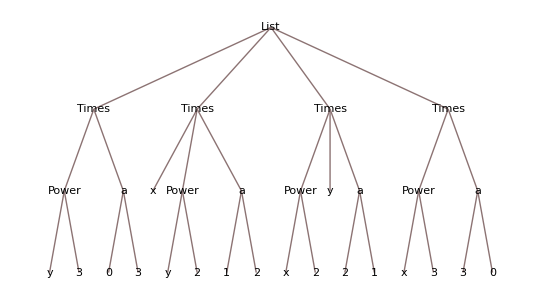

List

{x^3 a[3,0],x^2 y a[2,1],x y^2 a[1,2],y^3 a[0,3]}

{a[0],x a[1],x^2 a[2],x^3 a[3]}

{a[0],x a[1],x^2 a[2],x^3 a[3]}

{y^3 a[0,3],x y^2 a[1,4],x^2 y a[2,5],x^3 a[3,6]}

{y^3 a[0,3],x y^2 a[1,4],x^2 y a[2,5],x^3 a[3,6]}

```mathematica
n=3
(*a)*)
(*Первый способ*)
∑_(i=0)^n a[n-i,i] x^(n-i)y^i
∑_(i=0)^n a[n-i,i] x^(n-i)y^i//FullForm
∑_(i=0)^n a[n-i,i] x^(n-i)y^i//TreeForm
Head[∑_(i=0)^n a[n-i,i] x^(n-i)y^i]
List@@(∑_(i=0)^n a[n-i,i] x^(n-i)y^i)
List@@(∑_(i=0)^n a[n-i,i] x^(n-i)y^i)//FullForm
List@@(∑_(i=0)^n a[n-i,i] x^(n-i)y^i)//TreeForm
Head[List@@(∑_(i=0)^n a[n-i,i] x^(n-i)y^i)]
(*Второй способ*)
a[n-#,#] x^(n-#)y^#&/@Range[0,n]
(*б)*)
(*Первый способ*)
List@@(∑_(i=0)^n a[i] x^i)
(*Второй способ*)
a[#] x^#&/@Range[0,n]
(*в)*)
(*Первый способ*)
List@@(∑_(i=0)^n a[i,i+3] x^i y^(n-i))
(*Второй способ*)
a[#, #+3] x^# y^(n-#)&/@Range[0,n]
```

### Задание 1.3

Подберите одну из возможных формул n-го члена заданной числовой последовательности. Убедитесь в правильности построения, записав n-ый член в виде чистой функции и вычислив первые 7 членов последовательности. Постройте график зависимости значения члена последовательности от номера члена. Используйте функцию ListPlot. Вариант 9. 
Комментарии к решению: сначала я определяю формулу числовой последовательности, у моего варианта это будет ∑_(i=1)^n 99-i*25^. Затем пишу чистую функцию своей последовательности для того, чтобы свериться с условием и убедиться, что формулу ряда я подобрал правильно. В завершении строю график зависимости значения члена последовательности от номера члена, используя ListPlot вместе со свойством DataRange, указывающим диапазон координат x. Анализируя график утверждаю, что, чем больше номер n члена моей последовательности, тем меньше его значение по этому номеру.

6

{99,74,49,24,-1,-26,-51}

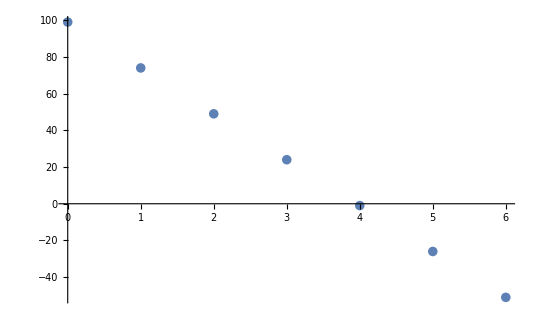

```mathematica
n=6
99-#*25&/@Range[0,n]
ListPlot[99-#*25&/@Range[0,n],DataRange->{0,n}]
```

### Задание 1.4

Приведите заданное рациональное уравнение к виду (P(x))/(Q(x))=0, при этом числитель P(x) должен быть разложен на множители, до линейных и квадратичных с отрицательным дискриминантом множителей. Используйте функции FullForm, Head, Numerator, Denominator, Factor, Together. Постройте выражение-однострочник, содержащее чистые функции в постфиксной записи и выполняющее поставленную задачу.  Вариант 9. 
Комментарии к решению: задание выполняю пошагово для получения итогового результата. Сначала я пробую привести к общему знаменателю и сложить две дроби в левой части уравнения с помощью функции Together. Теперь у меня есть одна дробь и слева, и справа. Так как теперь head’ом моего выражения является Equal (равенство), то я пробую заменить его, как в примере, сначала на Plus, используя функцию Apply. Теперь я получаю выражение, содержащее сумму двух дробей. Но, перенося в левую часть, я меняю знак на противоположный. Тогда с помощью функции MapAt я применю свой “-” к дроби, которую переносил из правой части. Из-за особенностей Mathematica, дробь будет стоять на первой позиции, после применения функций Together и Apply. Итоговое выражение складываю снова с помощью функции Together и получаю финальную дробь, представленную ниже.

```mathematica
(4x)/(8 x^3+1)+1/(16 x^4-4 x^2+4x-1)==2/(4 x^2+2x-1)//Together//Apply[Plus,#]&//MapAt[-#&,#, 1]&//Together
```

(-1-2 x+8 x^2)/((1+2 x) (1-2 x+4 x^2) (-1+2 x+4 x^2))

## 2. Анализ структуры выражения.

### Задание 2.1

Изучите возможности исследования структуры заданного выражения посредством функций FullForm, TreeForm, Level, Depth. Вариант 9. 
Комментарии к решению: вначале я ассоциирую своё выражение с переменной expr1 и проверяю с помощью функции Definition. Далее представляю своё выражение в виде дерева, а так же получаю полную форму. Расмотрим полученное дерево: в корневом узле находится head, в нашем случае им является Times. Два смежных ребра соединяют head с его аргументами, которые являются составными выражениями и в свою очередь “разбиваются” дальше. Хорошо, что же с полной формой? Изучив то, как выглядит полная форма моего выражения я пришёл к выводу, что это есть ни что иное, как то же самое дерево, НО записанное с помощью метода прямого обхода для деревьев. Суть метода состоит в том, что:
1) Проверяем, не является ли текущий узел пустым или null.
2) Показываем поле данных корня (или текущего узла).
3) Обходим левое поддерево рекурсивно, вызвав функцию прямого обхода.
4) Обходим правое поддерево рекурсивно, вызвав функцию прямого обхода.
-Graphics-
И действительно, присмотревшись внимательно к примеру ниже можно убедиться в верности моего утверждения.
Выводя каждый из уровней дерева по отдельности я наблюдаю, что аргументы действительно выглядят верно с первого по седьмой уровень, так же, как они и выглядят в дереве. 
А теперь пробую вывести нулевой уровень дерева. В итоге я получаю... Не изменённое своё выражение в изначальной форме. Почему же так вышло? Давайте попробуем подвести на корневой узел выведенного дерева указателем мыши, мы увидим тоже самое наше выражение в изначальной форме. А это есть ни что иное, как стандартная нотация, соответствующая корневому узлу, который уже в свою очередь является head’ом нашего выражения. То есть, выводя нулевой уровень выражения, мы выводим head нашего выражения. Так как head находится на нулевом уровне всегда, мы всегда его и будем получать, выводя нулевой уровень выражения.
Количество уровней выражения вычисляю с помощью функции Depth. В итоге получаю глубину равную значению 8. Но ведь уровней 7, как же так вышло, что мы получили 8? Дело в том, что мы считаем уровни с нуля, с корневого узла выражения, поэтому получем индекс последнего уровня всегда на единицу меньше глубины, которая просчитывается стандартно. По сути так же, как если бы мы работали с одним из современных ЯП, с индексацией массивов с нуля. Таким образом все возможные подвыражения выражения расположены на уровнях от 0 до Depth[expr1] - 1. В нашем случае уровней 7, как и было сказано ранее, дальше будут выводиться пустые списки.
Теперь посмотрим на выводы конкретных команд:
1) Level[expr1,{Depth[expr1]-1}] - как нам уже известно, функция Depth[expr1]-1 отработает с результатом 7. А значит мы просто выводим последний уровень нашего выражения.
2) Level[expr1,{−1}] - выводит все атомарные выражения нашего выражения.
3) Level[expr1,{Depth[expr1]-2}] - выводит предпоследний уровень нашего выражения: 6.
4) Level[expr1,{−2}] - выводит все подвыражения, имеющие глубину 2.

ⅇ^(a x) (1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2)))

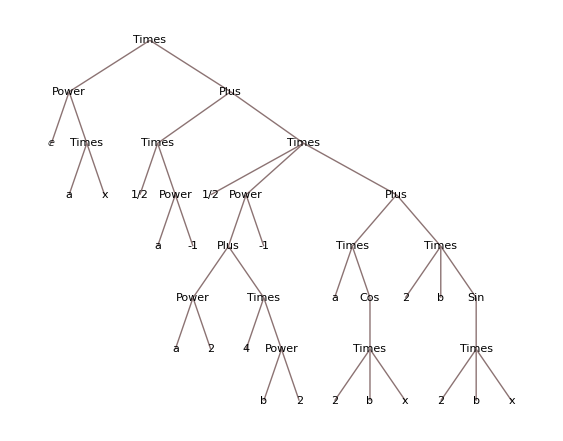

Times[Power[E,Times[a,x]],Plus[Times[Rational[1,2],Power[a,-1]],Times[Rational[1,2],Power[Plus[Power[a,2],Times[4,Power[b,2]]],-1],Plus[Times[a,Cos[Times[2,b,x]]],Times[2,b,Sin[Times[2,b,x]]]]]]]

{ⅇ^(a x) (1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2)))}

{ⅇ^(a x),1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))}

{ⅇ,a x,1/(2 a),(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))}

{a,x,1/2,1/a,1/2,1/(a^2+4 b^2),a Cos[2 b x]+2 b Sin[2 b x]}

{a,-1,a^2+4 b^2,-1,a Cos[2 b x],2 b Sin[2 b x]}

{a^2,4 b^2,a,Cos[2 b x],2,b,Sin[2 b x]}

{a,2,4,b^2,2 b x,2 b x}

{b,2,2,b,x,2,b,x}

{}

{}

8

{b,2,2,b,x,2,b,x}

{ⅇ,a,x,1/2,a,-1,1/2,a,2,4,b,2,-1,a,2,b,x,2,b,2,b,x}

{a,2,4,b^2,2 b x,2 b x}

{a x,1/a,a^2,b^2,2 b x,2 b x}

```mathematica
expr1=ⅇ^(a*x)(1/(2a)+(a*Cos[2b*x]+2b*Sin[2b*x])/(2(a^2+4 b^2)))
?expr1
TreeForm[expr1]
FullForm[expr1]
Level[expr1,{0}]
Level[expr1,{1}]
Level[expr1,{2}]
Level[expr1,{3}]
Level[expr1,{4}]
Level[expr1,{5}]
Level[expr1,{6}]
Level[expr1,{7}]
Level[expr1,{8}]
Level[expr1,{9}]
Depth[expr1]
Level[expr1,{Depth[expr1]-1}]
Level[expr1,{−1}]
Level[expr1,{Depth[expr1]-2}]
Level[expr1,{−2}]
```

### Задание 2.2

Форматируйте структуру заданного выражения, используя функции Head, Table, MatrixForm. Используйте чистые (анонимные, безымянные) функции и функцию Map.
Комментарии к решению: для начала я сравниваю функцию Table и оператор Do. Table является функцией, предназначенной для построения списков и матриц. Мы можем задать формулу общего члена и и нужное количество итераций. В качестве формулы может быть любое выражение: встроенная функция, своя функция, комбинация функций. Функция реализует конструкцию повторения, вычисляет выражение при каждом значении локальной переменной итератора. Множество значений, которые принимает локальная переменная, как раз и описывает итератор.
Do - способ создания цикла с заранее известным количеством шагов. 
Ниже я привожу простейшие примеры использования Do и Table. Как я считаю, они отличаются тем, что в Do мы можем контролировать процесс, сам цикл. Меняя тело цикло под свои нужды. А используя Table, мы просто выводим значение выражения, в зависимости от значения переменной итерации.
Head/@Level[expr1,{1,Depth[expr1]-1}] - применяю функцию Head к каждому из подвыражений нашего выражения expr1. Перед этим для проверки просто вывожу все аргументы. Я заметил, что выводятся они способом обратного обхода дерева из задания 2.1. Сам способ выполняется следующим образом:
1) Проверяем, не является ли текущий узел пустым или null.
2) Обходим левое поддерево рекурсивно, вызвав функцию обратного обхода.
3) Обходим правое поддерево рекурсивно, вызвав функцию обратного обхода.
4) Показываем поле данных корня (или текущего узла).
-Graphics-

```mathematica
(*Простой пример использования оператора Do*)
M=RandomInteger[{-5,5},10]
result=0;
Do[result=result+M[[i]],{i,1,10}]
result
(*Простой пример использования функции Table*)
Table[i^2,{i,10}]
(*Список из уровней, вывожу без нулевого элемента head в виде матрицы*)
Table[Level[expr1,{i}],{i,1,Depth[expr1]-1}]//MatrixForm
(*Получаю head каждого из подвыражений всех уровней*)
Level[expr1,{1,Depth[expr1]-1}]
Head/@Level[expr1,{1,Depth[expr1]-1}]
(*Список списков head'ов в виде матрицы*)
Table[Head/@Level[expr1,{i}],{i,1,Depth[expr1]-1}]//MatrixForm
(*Список из элементов и их head'ов*)
Table[{Head[#],#}&/@Level[expr1,{i}],{i,1,Depth[expr1]-1}]
Table[MatrixForm[{Head[#],#}&/@Level[expr1,{i}],TableDirections->{Row,Column}],{i,1,Depth[expr1]-1}]
```

{1,4,2,2,5,3,5,1,-4,3}

22

{1,4,9,16,25,36,49,64,81,100}

({ⅇ^(a x),1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))}
{ⅇ,a x,1/(2 a),(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))}
{a,x,1/2,1/a,1/2,1/(a^2+4 b^2),a Cos[2 b x]+2 b Sin[2 b x]}
{a,-1,a^2+4 b^2,-1,a Cos[2 b x],2 b Sin[2 b x]}
{a^2,4 b^2,a,Cos[2 b x],2,b,Sin[2 b x]}
{a,2,4,b^2,2 b x,2 b x}
{b,2,2,b,x,2,b,x})

{ⅇ,a,x,a x,ⅇ^(a x),1/2,a,-1,1/a,1/(2 a),1/2,a,2,a^2,4,b,2,b^2,4 b^2,a^2+4 b^2,-1,1/(a^2+4 b^2),a,2,b,x,2 b x,Cos[2 b x],a Cos[2 b x],2,b,2,b,x,2 b x,Sin[2 b x],2 b Sin[2 b x],a Cos[2 b x]+2 b Sin[2 b x],(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2)),1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))}

{Symbol,Symbol,Symbol,Times,Power,Rational,Symbol,Integer,Power,Times,Rational,Symbol,Integer,Power,Integer,Symbol,Integer,Power,Times,Plus,Integer,Power,Symbol,Integer,Symbol,Symbol,Times,Cos,Times,Integer,Symbol,Integer,Symbol,Symbol,Times,Sin,Times,Plus,Times,Plus}

({Power,Plus}
{Symbol,Times,Times,Times}
{Symbol,Symbol,Rational,Power,Rational,Power,Plus}
{Symbol,Integer,Plus,Integer,Times,Times}
{Power,Times,Symbol,Cos,Integer,Symbol,Sin}
{Symbol,Integer,Integer,Power,Times,Times}
{Symbol,Integer,Integer,Symbol,Symbol,Integer,Symbol,Symbol})

{{{Power,ⅇ^(a x)},{Plus,1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))}},{{Symbol,ⅇ},{Times,a x},{Times,1/(2 a)},{Times,(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))}},{{Symbol,a},{Symbol,x},{Rational,1/2},{Power,1/a},{Rational,1/2},{Power,1/(a^2+4 b^2)},{Plus,a Cos[2 b x]+2 b Sin[2 b x]}},{{Symbol,a},{Integer,-1},{Plus,a^2+4 b^2},{Integer,-1},{Times,a Cos[2 b x]},{Times,2 b Sin[2 b x]}},{{Power,a^2},{Times,4 b^2},{Symbol,a},{Cos,Cos[2 b x]},{Integer,2},{Symbol,b},{Sin,Sin[2 b x]}},{{Symbol,a},{Integer,2},{Integer,4},{Power,b^2},{Times,2 b x},{Times,2 b x}},{{Symbol,b},{Integer,2},{Integer,2},{Symbol,b},{Symbol,x},{Integer,2},{Symbol,b},{Symbol,x}}}

{(Power | Plus
ⅇ^(a x) | 1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))),(Symbol | Times | Times | Times
ⅇ | a x | 1/(2 a) | (a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))),(Symbol | Symbol | Rational | Power | Rational | Power | Plus
a | x | 1/2 | 1/a | 1/2 | 1/(a^2+4 b^2) | a Cos[2 b x]+2 b Sin[2 b x]),(Symbol | Integer | Plus | Integer | Times | Times
a | -1 | a^2+4 b^2 | -1 | a Cos[2 b x] | 2 b Sin[2 b x]),(Power | Times | Symbol | Cos | Integer | Symbol | Sin
a^2 | 4 b^2 | a | Cos[2 b x] | 2 | b | Sin[2 b x]),(Symbol | Integer | Integer | Power | Times | Times
a | 2 | 4 | b^2 | 2 b x | 2 b x),(Symbol | Integer | Integer | Symbol | Symbol | Integer | Symbol | Symbol
b | 2 | 2 | b | x | 2 | b | x)}

### Задание 2.3

Изучите возможности исследования структуры выражения посредством функций AtomQ, Position, Part, Take, Length. Используйте заданное выражение в качестве примера.

Times[Power[E,Times[a,x]],Plus[Times[Rational[1,2],Power[a,-1]],Times[Rational[1,2],Power[Plus[Power[a,2],Times[4,Power[b,2]]],-1],Plus[Times[a,Cos[Times[2,b,x]]],Times[2,b,Sin[Times[2,b,x]]]]]]]

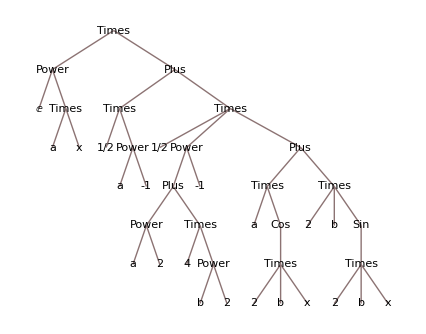

{{1,2,2},{2,2,3,1,2,1,3},{2,2,3,2,3,1,3}}

{{1,2,2},{2,2,3,1,2,1,3},{2,2,3,2,3,1,3}}

{{1,2,1},{2,1,2,1},{2,2,2,1,1,1},{2,2,3,1,2}}

{{1,2,1},{2,1,2,1},{2,2,2,1,1,1},{2,2,3,1,1}}

{{2,2,2,1,2,2,1},{2,2,3,1,2,1,2},{2,2,3,2,2},{2,2,3,2,3,1,2}}

{{2,2,2,1,2,2,1},{2,2,3,1,2,1,2},{2,2,3,2,2},{2,2,3,2,3,1,2}}

x

b

{{2,1}}

{1/(2 a)}

{True,False,False,False}

{True,True,True,False,True,False,False}

{{1,1}}

{{1,2,1},{2,1,2,1},{2,2,2,1,1,1},{2,2,3,1,1}}

{{1,2,2},{2,2,3,1,2,1,3},{2,2,3,2,3,1,3}}

{{2,1,1},{2,2,1}}

ⅇ

a

x

1/2

1/2

```mathematica
(*Определяю позицию каждого из выражений. Сначала ручками через анализ FulForm, потом с помощью Position для проверки*)
FullForm[expr1]
TreeForm[expr1]
(*Определяю позицию для x*)
List1={{1,2,2},{2,2,3,1,2,1,3},{2,2,3,2,3,1,3}}
Position[expr1,x]
(*Определяю позицию для a*)
List2={{1,2,1},{2,1,2,1},{2,2,2,1,1,1},{2,2,3,1,2}}
Position[expr1,a]
(*Определяю позицию для b*)
List2={{2,2,2,1,2,2,1},{2,2,3,1,2,1,2},{2,2,3,2,2},{2,2,3,2,3,1,2}}
Position[expr1,b]
(*Извлеку два последних аргумента из исходного выражения с помощью функции Part. Это выражения b и x, позиции которых мы узнали выше*)
expr1[[2,2,3,2,3,1,3]]
expr1[[2,2,3,2,3,1,2]]
(*Предпоследнее выражение второго уровня извлеку с помощью функции Take, указывая спецификатор последовательности*)
Position[expr1,1/(2*a)]
(*Не получилось использовать Take. Sad. upd, получилось, думаю, что так можно*)
Take[Level[expr1,2],{4,4,3}]
(*Определим, имеются ли атомарные выражения среди подвырожений первого и второго уровней*)
AtomQ/@Level[expr1,{2}]
AtomQ/@Level[expr1,{3}]
(*Определили. Извлечём их с помощью функций Position и Part*)
Position[expr1,ⅇ]
Position[expr1,a]
Position[expr1,x]
Position[expr1,1/2]
(*Получаю координаты моих атомов:{1,1}, {1,2,1}, {1,2,2}, {2,1,1},{2,2,1} (e, a, x, 1/2)*)
expr1[[1,1]]
expr1[[1,2,1]]
expr1[[1,2,2]]
expr1[[2,1,1]]
expr1[[2,2,1]]
(*Вохможно есть менее костыльный способ написать функцию и каким-то образом узнавать значения координат атомов на уровнях, сразу вставляя их  в функцию Part, но я не обладаю такими технологиями.
Выводы про использование функций Part, Take, Position. Функции довольно простые в использовании, хотя по началу Take показалась мне слишком трудной для понимания, потому что я не использовал для неё список, как нужно, а пихал целое выражение. Но работать мне больше понравилось с Part, которыя в отличие от Take, даёт точный результат выражения по координатам, определить которые в свою очередь помогает функция Position. Take же рабтает с диапазоном списка, в котором бывает трудно выбрать какое-то одно конкретное выражение, так как мы лио проходимся по каждому его элементу, либо с шагом, не всегда удобным, и то, внося как минимум первую границу диапазона в результат, которая не всегда бывает нужна.*)
```